```mathematica
(*Data for distance ladder dependent measurements with uncertainties handled by Around,excluding SH0ES 2022*)distanceLadderDependent={{2019.1,Around[73.3,4.0]},{2020.0,Around[76.0,3.4]},{2021.2,Around[73.3,3.1]},{2021.3,Around[69.8,2.6]},{2021.4,Around[74.82,1.81]},{2021.5,Around[70.92,2.63]},{2022.1,Around[76.94,6.4]},{2022.1,Around[73.04,1.04]},{2022.1,Around[73.1,2.5]},{2023.1,Around[74.1,8]},{2023.2,Around[72.37,2.97]},{2023.2,Around[71.76,1.32]},{2023.25,Around[73.22,1.45]},{2023.3,Around[73.22,2.06]},{2024.0,Around[73.1,2.3]},{2024.2,Around[74.7,3.1]},{2024.4,Around[68.0,2.65]},{2024.3,Around[72.05,3.6]},{2024.4,Around[73.3,4.08]}};

distanceLadderIndependent={{2003.0,Around[61,21]},{2015.0,Around[66.0,6.0]},{2019.0,Around[74.2,1.6]},{2020.1,Around[67.4,4]},{2020.2,Around[73.9,3.0]},{2021.1,Around[68,7]},{2022.0,Around[65.9,3.0]},{2022.1,Around[69.6,5.5]},{2022.2,Around[64.8,2.4]},{2023.0,Around[85.4,31.5]},{2023.1,Around[72.9,2.15]},{2023.2,Around[71.5,3.7]},{2023.3,Around[66.6,3.8]},{2023.3,Around[71.5,3.1]},{2023.4,Around[62.4,4]},{2023.4,Around[67.2,6]},{2023.5,Around[66.7,5.3]},{2023.6,Around[67.0,3.6]},{2023.6,Around[68.8,11]},{2023.7,Around[59.1,3.5]},{2023.7,Around[65.5,6]},{2023.7,Around[75.46,5.3]},{2023.7,Around[77.1,7.2]},{2024.0,Around[65,18.5]},{2024.1,Around[69.9,12.65]},{2024.2,Around[70.0,4.8]},{2024.3,Around[65.1,3.5]},{2024.3,Around[69.88,0.93]},{2024.4,Around[71.8,8.8]},{2024.5,Around[67.37,0.96]},{2024.5,Around[66.3,3.7]}};

(*Function to calculate weighted mean and standard deviation*)
calculateWeightedMean[data_]:=Module[{h0Values,uncertainties,weights,weightedH0,weightedMeanH0,stdDeviation},h0Values=data[[All,2]]/. Around[value_,_]:>value;
uncertainties=data[[All,2]]/. Around[_,error_]:>error;
(*Calculate weights based on the uncertainties*)weights=1/(uncertainties^2);
(*Calculate weighted H0*)weightedH0=(h0Values*weights)/Total[weights];
(*Calculate the weighted mean of H0*)weightedMeanH0=Total[weightedH0];
(*Calculate the standard deviation of the weighted mean*)stdDeviation=Sqrt[1/Total[weights]];
(*Output the results*)<|"Weighted Mean H0"->weightedMeanH0,"Standard Deviation"->stdDeviation|>]

(*Calculate results for both datasets*)
resultsDependent=calculateWeightedMean[distanceLadderDependent];
resultsIndependent=calculateWeightedMean[distanceLadderIndependent];

(*Output the results*)
<|"Distance Ladder Dependent"->resultsDependent,"Distance Ladder Independent"->resultsIndependent|>
```

<|Distance Ladder Dependent→<|Weighted Mean H0→72.7616,Standard Deviation→0.503366|>,Distance Ladder Independent→<|Weighted Mean H0→69.0057,Standard Deviation→0.486032|>|>

```mathematica
Length[distanceLadderDependent]
```

19

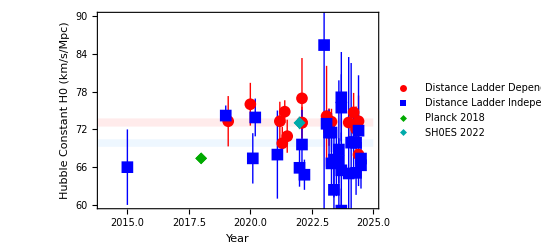

C:\Users\leand\Desktop\dl-tension\HubbleConstantPlot.pdf

```mathematica
(*Planck 2018 and SH0ES 2022 points*)
planck2018={2018,Around[67.4,0.5]};
sh0es2022={2022,Around[73.04,1.0]};

(*Create the plot using ListPlot*)
hubblePlot=ListPlot[{distanceLadderDependent,distanceLadderIndependent,{planck2018},{sh0es2022}},PlotStyle->{Red,Blue,{Darker[Green],PointSize[0.015]},{Darker[Cyan],PointSize[0.015]}},PlotMarkers->{{"●",12},{"■",12},{"◆",12},{"◆",12}},Frame->True,FrameLabel->{"Year","Hubble Constant H0 (km/s/Mpc)"},PlotRange->{{2014,2025},{60,90}},PlotLegends->{"Distance Ladder Dependent","Distance Ladder Independent","Planck 2018","SH0ES 2022"},IntervalMarkers->"Bars",IntervalMarkersStyle->{Red,Blue,Darker[Green],Darker[Cyan]},Joined->False,Prolog->{{Opacity[0.5,LightRed],Rectangle[{2010,73.1003-0.653403},{2025,73.1003+0.653403}]},{Opacity[0.5,LightBlue],Rectangle[{2010,69.8347-0.604},{2025,69.8347+0.604}]}}]

(*Export the plot to a PDF file*)
Export[FileNameJoin[{NotebookDirectory[],"HubbleConstantPlot.pdf"}],hubblePlot]
```

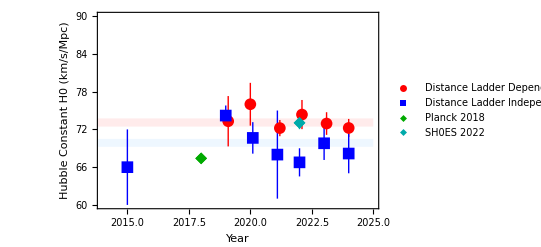

C:\Users\leand\Desktop\dl-tension\HubbleConstantPlotBinned.pdf

```mathematica
(*Function to merge points by year using the integer part of the year*)mergeDataByYear[data_List]:=Module[{grouped,averaged},(*Use Floor to take the integer part of the year before grouping*)grouped=GatherBy[data,Floor[#[[1]]]&];
averaged={#[[1,1]],Mean[#[[All,2]]]}&/@grouped;
Return[averaged];];

(*Merged data*)
mergedDistanceLadderDependent=mergeDataByYear[distanceLadderDependent];
mergedDistanceLadderIndependent=mergeDataByYear[distanceLadderIndependent];

(*Create the plot*)
hubblePlot=ListPlot[{mergedDistanceLadderDependent,mergedDistanceLadderIndependent,{planck2018},{sh0es2022}},PlotStyle->{Red,Blue,{Darker[Green],PointSize[0.015]},{Darker[Cyan],PointSize[0.015]}},PlotMarkers->{{"●",12},{"■",12},{"◆",12},{"◆",12}},Frame->True,FrameLabel->{"Year","Hubble Constant H0 (km/s/Mpc)"},PlotRange->{{2014,2025},{60,90}},PlotLegends->{"Distance Ladder Dependent","Distance Ladder Independent","Planck 2018","SH0ES 2022"},IntervalMarkers->"Bars",IntervalMarkersStyle->{Red,Blue,Darker[Green],Darker[Cyan]},Joined->False,Prolog->{{Opacity[0.5,LightRed],Rectangle[{2010,73.1003-0.653403},{2025,73.1003+0.653403}]},{Opacity[0.5,LightBlue],Rectangle[{2010,69.8347-0.604},{2025,69.8845+0.604}]}}]

(*Export the plot to a PDF file*)
Export[FileNameJoin[{NotebookDirectory[],"HubbleConstantPlotBinned.pdf"}],hubblePlot]
```

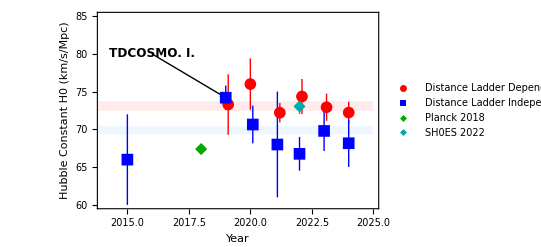

C:\Users\leand\Desktop\dl-tension\HubbleConstantBinnedPlot.pdf

```mathematica
(*Create the plot with specified adjustments*)hubblePlot=ListPlot[{mergedDistanceLadderDependent,mergedDistanceLadderIndependent,{planck2018},{sh0es2022}},PlotStyle->{Red,Blue,{Darker[Green],PointSize[0.015]},{Darker[Cyan],PointSize[0.015]}},PlotMarkers->{{"●",12},{"■",12},{"◆",12},{"◆",12}},Frame->True,FrameLabel->{"Year","Hubble Constant H0 (km/s/Mpc)"},PlotRange->{{2014,2025},{60,85}},(*Adjusted vertical range*)PlotLegends->{"Distance Ladder Dependent","Distance Ladder Independent","Planck 2018","SH0ES 2022"},IntervalMarkers->"Bars",IntervalMarkersStyle->{Red,Blue,Darker[Green],Darker[Cyan]},Joined->False,Prolog->{{Opacity[0.5,LightRed],Rectangle[{2010,73.1003-0.653403},{2025,73.1003+0.653403}]},{Opacity[0.5,LightBlue],Rectangle[{2010,69.8845-0.572741},{2025,69.8845+0.572741}]}},Epilog->{{Arrowheads[0.02],Arrow[{{2016,80},{2019,74.2}}]},(*Adjust the arrow to point from the new text position to the blue point of 2019*)Text[Style["TDCOSMO. I.","Times",Bold,12],{2016,80}]  (*Center the text at (2016,80) using Times font*)}]
Export[FileNameJoin[{NotebookDirectory[],"HubbleConstantBinnedPlot.pdf"}],hubblePlot]
```

```mathematica
(*Define the H0 measurements and their errors*)hubbleData={{59,3,11},(*{H0,statistical error,systematic error}*){75,7,0},(*Assuming no systematic error reported*){71,12,0},(*Assuming no systematic error reported*){75.8,5.2,2.8},{75.4,3.8,1.5}};

(*Calculate total errors by adding statistical and systematic errors in quadrature*)
totalErrors=Sqrt[#2^2+#3^2]&@@@hubbleData;

(*Calculate weights for each measurement (inverse of the square of total error)*)
weights=1/totalErrors^2;

(*Calculate the weighted mean of H0*)
weightedMeanH0=Total[(#[[1]]*weights[[#2]])&@@@Thread[{hubbleData,Range[Length[hubbleData]]}]]/Total[weights];

(*Calculate the mean uncertainty as the mean of the total errors*)
meanUncertainty=Mean[totalErrors];

(*Output the results*)
{weightedMeanH0,meanUncertainty}
```

{74.1592,8.0786}

```mathematica
Length[distanceLadderIndependent]
```

31

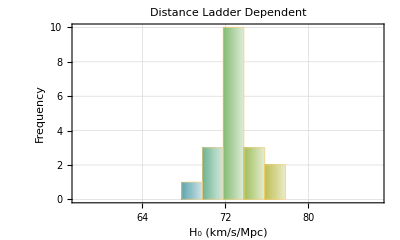

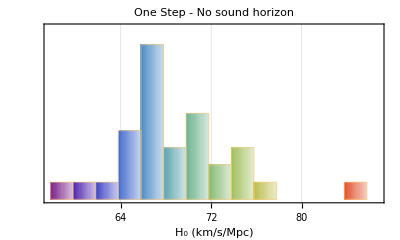

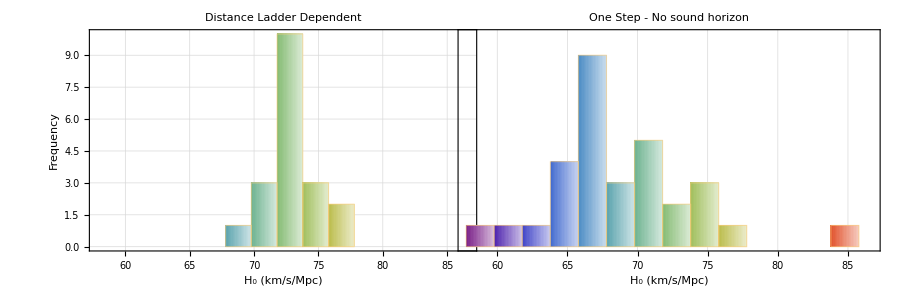

C:\Users\leand\Desktop\dl-tension\H0_Comparison.pdf

```mathematica
data1=distanceLadderDependent[[All,2]];
values1=N[data1[[All,1]]];

data2=distanceLadderIndependent[[All,2]];
values2=N[data2[[All,1]]];

minH0=Min[Min[values1],Min[values2]];
maxH0=Max[Max[values1],Max[values2]];

padding=(maxH0-minH0)*0.05;
plotRange={minH0-padding,maxH0+padding};

binWidth=2;
bins=Range[plotRange[[1]],plotRange[[2]],binWidth];

maxFreq=Max[HistogramList[values1,{bins}][[2]],HistogramList[values2,{bins}][[2]]];

colorFunction=ColorData["Rainbow"];
binColors=Table[colorFunction[x],{x,0,1,1/(Length[bins]-1)}];

histogramSettings={PlotRange->{{plotRange[[1]],plotRange[[2]]},{0,maxFreq}},Frame->True,FrameStyle->Directive[Black,12],PlotTheme->"Detailed",ChartStyle->binColors,ChartElementFunction->"FadingRectangle",ImageSize->400,AspectRatio->0.6};

pl1=Histogram[values1,{bins},PlotLabel->"Distance Ladder Dependent",FrameLabel->{{"Frequency",None},{Subscript["H",0] " (km/s/Mpc)",None}},Evaluate[histogramSettings]]

pl2=Histogram[values2,{bins},PlotLabel->"One Step - No sound horizon",FrameLabel->{{None,None},{Subscript["H",0] " (km/s/Mpc)",None}},FrameTicks->{{None,None},{Automatic,None}},Evaluate[histogramSettings]]

colorLegend=BarLegend[{"Rainbow",{minH0,maxH0}},LegendLabel->Subscript["H",0] " (km/s/Mpc)"];

combinedPlot=GraphicsRow[{pl1,pl2},Spacings->-75];

finalPlot=Legended[combinedPlot,Placed[colorLegend,Right]];

finalImage=Show[finalPlot,PlotRange->All,ImageSize->900,PlotLabel->Style["Comparison of "Subscript["H",0]" Measurements",16,Bold]]

(*Export the plot as a PDF file*)
Export[FileNameJoin[{NotebookDirectory[],"H0_Comparison.pdf"}],finalImage]
```

Kolmogorov-Smirnov Test Results:

p-value: 0.000101536

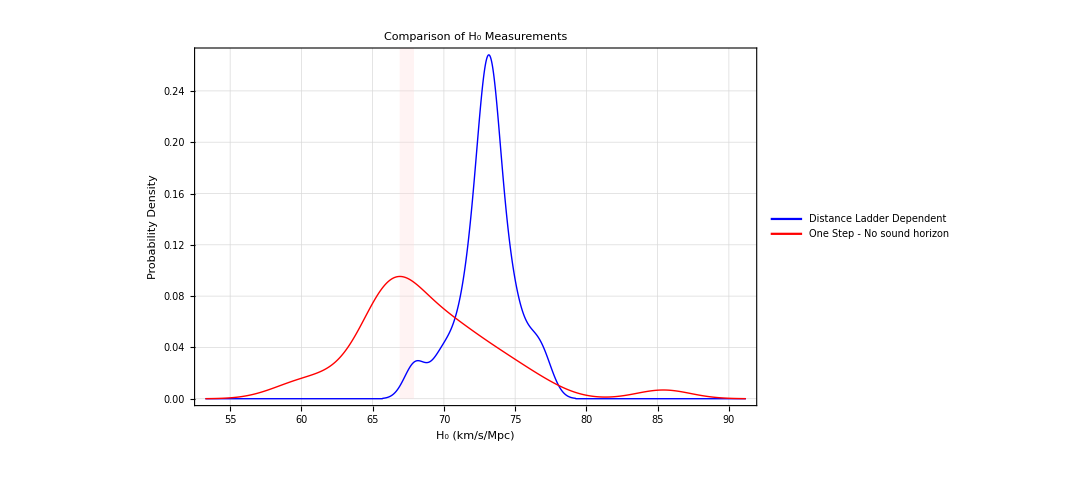

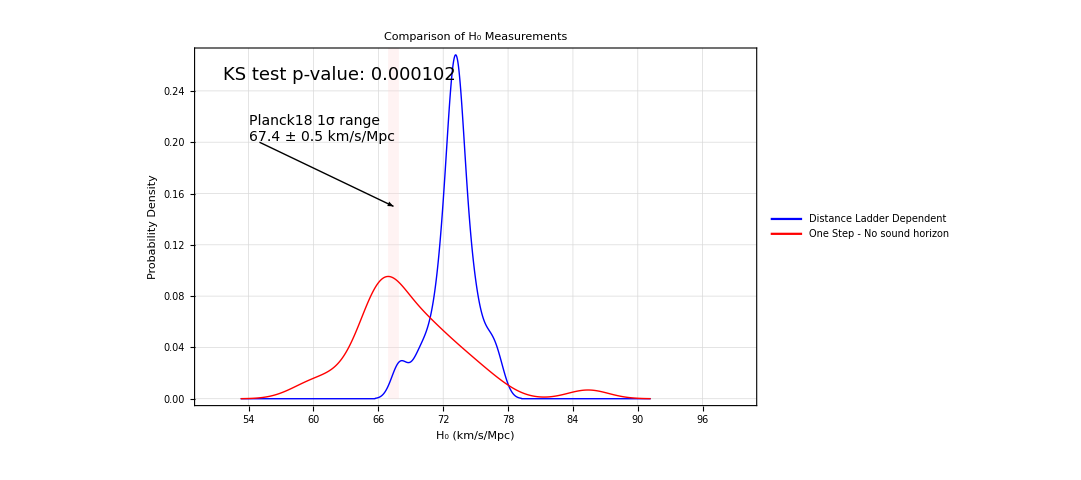

C:\Users\leand\Desktop\dl-tension\H0_SmoothHistogram_Comparison.pdf

```mathematica
dependent=N[distanceLadderDependent[[All,2,1]]];
independent=N[distanceLadderIndependent[[All,2,1]]];

ksTest=KolmogorovSmirnovTest[dependent,independent];

Print["Kolmogorov-Smirnov Test Results:"]
Print["p-value: ",ksTest]

(*Define Planck18 H₀ value and uncertainty*)
planckH0=67.4;(*Planck18 H₀ value*)planckUncertainty=0.5;(*Planck18 1σ uncertainty*)(*Create the vertical band*)planckBand=Rectangle[{planckH0-planckUncertainty,0},{planckH0+planckUncertainty,1}];

plot=SmoothHistogram[{dependent,independent},PlotRange->All,Frame->True,FrameLabel->{Style[Subscript["H",0] " (km/s/Mpc)",16],Style["Probability Density",16]},PlotLabel->Style["Comparison of "Subscript["H",0]" Measurements",16,Bold],PlotStyle->{{Thick,Blue},{Thick,Red}},PlotLegends->Placed[LineLegend[{Style["Distance Ladder Dependent",16],Style["One Step - No sound horizon",16]},LegendFunction->Frame],{0.75,0.8}],ImageSize->800,AspectRatio->0.6,BaseStyle->{FontFamily->"Times",FontSize->16},AxesStyle->Directive[Black,16],FrameStyle->Directive[Black,16],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],Prolog->{Opacity[0.3],LightRed,planckBand}]

(*Add KS test result to the plot*)
ksAnnotation=Text[Style["KS test p-value: "<>ToString[NumberForm[ksTest,{7,6}]],18],Scaled[{0.05,0.95}],{-1,1}];

(*Create arrow and label for Planck18 band*)
planckArrow=Arrow[{{55,0.2},{planckH0,0.15}}];
planckLabel=Text[Style["Planck18 1σ range\n"<>ToString[planckH0]<>" ± "<>ToString[planckUncertainty]<>" km/s/Mpc",14],{54,0.21},{-1,0}];

(*Combine everything*)
finalPlot=Show[plot,Epilog->{ksAnnotation,planckArrow,planckLabel},PlotRange->{{50,100},All}  (*Adjust x-range as needed*)]

(*Export the plot as a PDF file*)
Export[FileNameJoin[{NotebookDirectory[],"H0_SmoothHistogram_Comparison.pdf"}],finalPlot]
```